# PeterBurbery/BooleanLogic

Work with logical functions and boolean values

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Logic.nb"DocumentationEnglishGuidesLogic.nb

"ReferencePages"

"Symbols"

"BooleanCompose.nb"DocumentationEnglishReferencePagesSymbolsBooleanCompose.nb

"BooleanStructureData.nb"DocumentationEnglishReferencePagesSymbolsBooleanStructureData.nb

"BooleanTruthInputData.nb"DocumentationEnglishReferencePagesSymbolsBooleanTruthInputData.nb

"FindBooleanAlternative.nb"DocumentationEnglishReferencePagesSymbolsFindBooleanAlternative.nb

"InverseBoole.nb"DocumentationEnglishReferencePagesSymbolsInverseBoole.nb

"TruthTable.nb"DocumentationEnglishReferencePagesSymbolsTruthTable.nb

"VennDiagram.nb"DocumentationEnglishReferencePagesSymbolsVennDiagram.nb

"Tutorials"

"Kernel"

"BooleanLogic.wl"KernelBooleanLogic.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This paclet contains helpful functions for boolean logic. I give credit to the authors of FindBooleanAlternative, Stephen Wolfram and Nikolay Murzin. I want to compile helpful functions for logic into one place.

### Details

The picture has William of Ockham in the center, who formulated what is now known as De Morgan's Laws. William of Ockham was a theologian who formulated Ockham's razor and studied ternary logic.

I have several functions that I want to add but don't know how to program. I aim to make functions to find affine boolean functions, bent boolean functions, canalizing boolean functions, Horn boolean functions, Krom boolean functions, self-dual boolean functions, definite Horn boolean functions, symmetric boolean functions, threshold boolean functions and unate boolean functions. I learned about these types of boolean functions in the Art of Computer Programming Volume 4A by Donald Knuth.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Find an alternative form of p implies q and r with xor and nand:

```mathematica
FindBooleanAlternative[(P⇒Q)∧R,{Xor,Nand}]
```

(Q⊼R)⊼(R⊼(P⊼P))

Find seven other alternatives:

```mathematica
FindBooleanAlternative[(P⇒Q)∧R,{Xor,Nand},7]
```

{(Q⊼R)⊼(R⊼(P⊼P)),(Q⊼R)⊼(R⊼(P⊼R)),(Q⊼R)⊼(R⊼(R⊼P)),(Q⊼R)⊼(R⊼(P⊻R)),(Q⊼R)⊼((P⊼P)⊼R),(Q⊼R)⊼((P⊼R)⊼R),(Q⊼R)⊼((R⊼P)⊼R)}

Make a Venn diagram for b, c, and d:

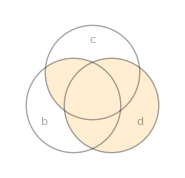

```mathematica
VennDiagram[(b∧c)∨d]
```

Add the input e to the Venn Diagram:

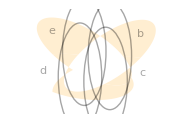

```mathematica
VennDiagram[b⊻(c∧d∨e)]
```

VennDiagram can accept up to 5 variables:

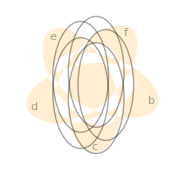

```mathematica
VennDiagram[Xor[b,c,d,e,f]]
```

Make a Venn diagram using BooleanFunction as input:

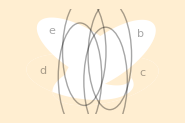

```mathematica
VennDiagram[BooleanFunction[RandomInteger[2^(2 4)],4][b,c,d,e]]
```

Create a Venn diagram by using sets as input:

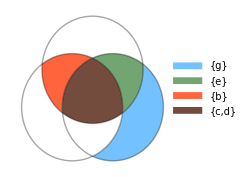

```mathematica
VennDiagram[{{b,c,d},{b,c,d,e},{d,c,e,g}}]
```

Create a Venn diagram by using Not and Or canonical normal form as input:

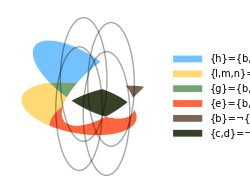

```mathematica
VennDiagram[{{b,c,d},{b,c,d,e},{d,c,e,g,l,m,n},{c,d,g,h}},"EquationForm"->"NOR"]
```

```mathematica
VennDiagram[{{b,c,d},{b,c,d,e},{d,c,e,g,l,m,n},{c,d,g,h}},"DiagramLegends"->"MouseOver","EquationForm"->"NOR"]
```

-Graphics-

Find information on a boolean function's structure:

```mathematica
BooleanStructureData[Xor[b,c,d,e]]
```

<|truth-table→{False,True,True,False,True,False,False,True,True,False,False,True,False,True,True,False},truth-vector→{0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0},input-variables→{b,c,d,e},positive-unate-monotone→False,negative-unate→False|>

Find information on the output given true inputs and false inputs, including whether the problem is satisfiable. This is helpful when working on the NP-complete problem 3SAT:

```mathematica
BooleanTruthInputData[BooleanFunction[RandomInteger[2^(2  3)],3]]
```

<|satisfiable→True,true-outputs-count→2,input-that-makes-output-true→{{False,True,False},{False,False,True}},tautology→False|>

Evaluate the NP complete 17SAT problem:

```mathematica
BooleanTruthInputData[BooleanFunction[RandomInteger[2^(2 17)],17]]//Short[#,9]&
```

<|satisfiable→True,true-outputs-count→16,input-that-makes-output-true→{{False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True},{False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,True},{False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,False},{False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True},«5»,{False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False},{False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False}},tautology→False|>

Generate a truth table for a function with 4 inputs:

```mathematica
TruthTable[b⊻c∨d∧e]//TraditionalForm
```

b | c | d | e | (b⊻c)∨(d∧e)
True | True | True | True | True
True | True | True | False | False
True | True | False | True | False
True | True | False | False | False
True | False | True | True | True
True | False | True | False | True
True | False | False | True | True
True | False | False | False | True
False | True | True | True | True
False | True | True | False | True
False | True | False | True | True
False | True | False | False | True
False | False | True | True | True
False | False | True | False | False
False | False | False | True | False
False | False | False | False | False

Use 1 and 0 in place of true and false, respectively:

```mathematica
TruthTable[b⊻c∨d∧e,"Symbols"->{1,0}]//TraditionalForm
```

b | c | d | e | (b⊻c)∨(d∧e)
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0

### Scope

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/boolean-logic

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

logic

boolean logic

ternary logic

Venn diagrams

Ockham's razor

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

FindBooleanAlternative

VennDiagram

InverseBoole

### Original Source References and Attributions

Source, reference or citation information

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies <+$Path+>, <+Directory+>, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public <+ResourceObject+> content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of <+SystemCredential+>Click for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via <+ExternalEvaluate+>
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes